# Učení RBF sítě Demonstrace pokrytí vstupních dat RBF sítí.

## Načtení knihovny NeuralNetworks

Nejdříve načteme knihovnu neuronových sítí.

```mathematica
<< NeuralNetworks`
```

Pokud pracujete v Mathematice 8.0, vypněte ještě zobrazování chybové hlášky Remove::rmnsm. Tuto hlášku vyhazují funkce knihovny NeuralNetworks. Na funkci knihovny toto nemá žádný vliv.

```mathematica
Off[Remove::rmnsm]
```

## Příprava trénovacích dat

Pokrytí vstupních budeme předvádět na klasifikaci do dvou tříd. Data budeme mít jednoduchá dvoudimenzionální, která obsahují dva dobře oddělené shluky dat, každý shluk reprezentuje jednu třídu.
Vygenerujeme tedy tyto dva shluky dat.

```mathematica
values=25;
cluster1 =RandomReal[{1,3},{values,2}];
cluster2=RandomReal[ {5,7},{values,2}];
inData = Join[cluster1,cluster2];
outcluster1=ConstantArray[{1,0},{values}];
outcluster2 = ConstantArray[{0,1},{values}];
outData= Join[outcluster1,outcluster2];
```

Takto vypadají naše vynerovaná vstupní data.

```mathematica
inData
```

{{1.61533,1.2154},{2.44512,1.03579},{1.72985,1.40565},{1.5098,1.21416},{1.70882,2.71144},{1.20908,2.85919},{1.52142,2.83582},{2.08724,2.5803},{1.12541,2.90177},{1.96879,2.00279},{2.56144,1.57805},{2.28818,1.02121},{2.06871,1.66453},{2.90321,1.78507},{2.96618,2.15481},{1.97447,1.5407},{1.402,2.75689},{2.42398,2.26889},{1.65997,1.92214},{2.77695,2.75386},{2.96259,1.22775},{2.02555,1.41764},{2.50297,1.25257},{2.46471,2.56758},{2.56677,2.17213},{6.91778,6.98777},{6.17599,6.17779},{5.26315,5.47677},{5.62199,5.61119},{6.14786,5.34541},{5.82785,6.30002},{5.72428,5.91206},{6.89239,6.59926},{5.75012,5.63298},{6.40214,5.46511},{6.94496,5.81564},{6.22421,6.36069},{6.3738,5.08648},{6.13449,5.71532},{6.42589,6.70088},{5.91109,6.72216},{6.7736,6.36498},{6.28421,5.01286},{5.48173,6.57286},{5.25735,6.56085},{6.6407,6.35052},{5.38443,6.27155},{5.6784,5.82632},{5.37911,5.19267},{6.51705,6.89553}}

A takto vypadají data výstupní.

```mathematica
outData
```

{{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1}}

Vygenerovaná data si můžeme zobrazit pro lepší představu zobrazit. Každá třída dat má v grafu jinou bavu.

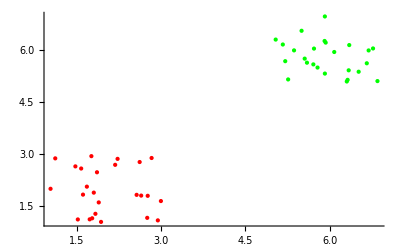

```mathematica
ListPlot[{cluster1,cluster2},PlotStyle->{Red,Green}]
```

Po vygenerování dat můžeme začít učit síť.

## Učení RBF sítě

Tato jednoduchá data budeme chtít klasifikovat pomocí RBF sítě s jedním RBF neuronem, dvěma vstupy a dvěma výstupy.
Vytvoříme RBF síť podle popisu výše.

```mathematica
net=InitializeRBFNet[inData,outData,1,RandomInitialization->True, OutputNonlinearity->Sigmoid]
```

RBFNet[{{w1, λ, w2}, χ},{Neuron → Exp, FixedParameters → None, AccumulatedIterations → 0, CreationDate → {2011, 3, 15, 16, 50, 12.154619}, OutputNonlinearity → Sigmoid, NumberOfInputs → 2}]

Zobrazíme si informace o sítí. Tím se ujistíme že síť je opravdu taková jakou jsme chtěli.

```mathematica
NetInformation[net]
```

Radial Basis Function network. Created 2011-3-15 at 16:50. The network has 2 inputs and 2 outputs.  It consists of 1 basis function of Exp type. The network has a linear submodel. There is a nonlinearity at the output of type Sigmoid.

Naučíme vytvořenou síť na našich datech.

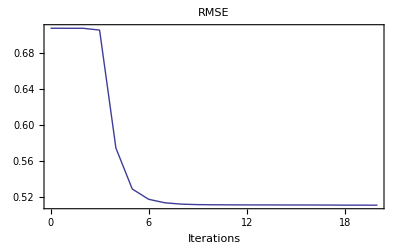

```mathematica
{net2,record}=NeuralFit[net,inData,outData,20];
```

Podívejme se jak naše síť klasifikuje data. Vidíme, že data jsou lineárně separabilní a síť je skutečně rozděluje přímkou.

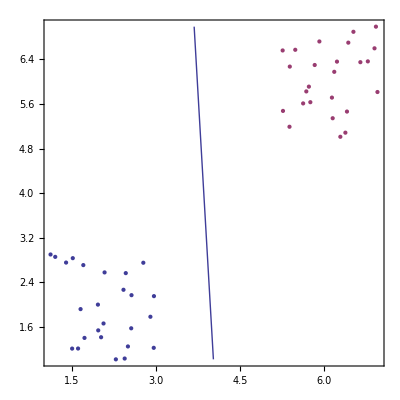

```mathematica
NetPlot[net2,inData,outData, DataFormat->Classifier]
```

## Výstup RBF neuronu

Nyní se podíváme na “vnitřnosti” neuronové sítě. Naše síť obsahuje jeden RBF neuron, mohlo by být zajímavé zjistit jakou oblast dat tento neuron pokrývá.
Nejprve upravíme síť aby vracela námi požadovaný výstup.

```mathematica
net3=net2;(*nechceme si rozbít původní síť*)
net3[[1,1,3]]=Append[IdentityMatrix[1],{0}];(*změna matice vah na identidkou matici*)
net3=NeuronDelete[net3,{0,0}];(*odstranění lineární části*)
```

A zobrazíme výstup.

```mathematica
gauss=Plot3D[net3[{x,y}][[1]],{x,-5,9},{y,-5,9},PlotRange->All]
```

-Graphics3D-

Ještě přidáme do grafu vstupní data.

```mathematica
cluster13d=cluster1/.{x_?NumberQ,y_?NumberQ}->{x,y,0.501};
cluster23d=cluster2/.{x_?NumberQ,y_?NumberQ}->{x,y,0.501};
data3d=ListPointPlot3D[{cluster13d,cluster23d},PlotStyle->{Red,Green},PlotStyle->PointSize[Large]];
Show[gauss,data3d]
```

-Graphics3D-